```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]],"Data"]];
Clear[AllFiles,FileData1,len1,f];AllFiles=Sort[FileNames["*.csv"]];len1=Length[AllFiles];
For[i=1,i≤len1,i++,{f=Import[AllFiles[[i]]];FileData1[i]=Take[f,{1,-1}],Clear[f]}];
```

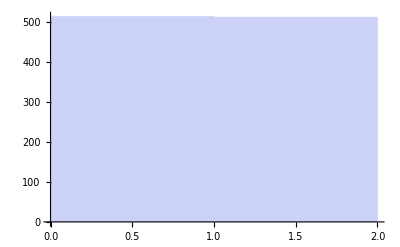
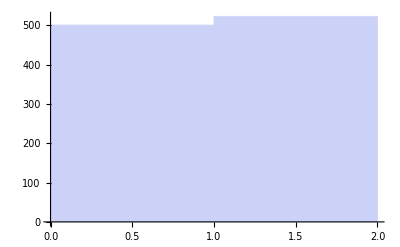
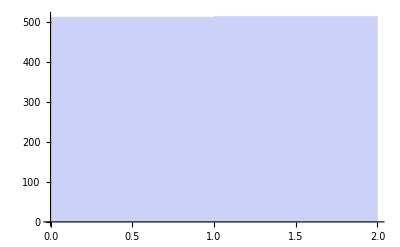
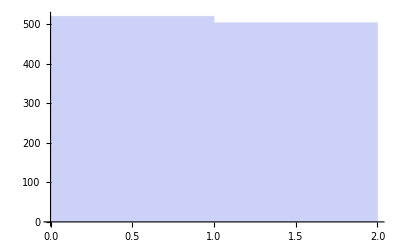
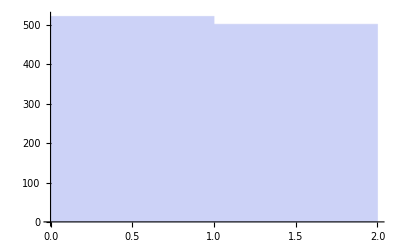
{-Graphics-,-Graphics-,-Graphics- -Graphics-,-Graphics-,-Graphics-}

```mathematica
{Histogram[FileData1[1][[1]]],Histogram[FileData1[1][[2]]],Histogram[FileData1[1][[3]]]Histogram[FileData1[1][[4]]],Histogram[FileData1[1][[5]]],Histogram[FileData1[1][[6]]]}
```

```mathematica
Vv={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
Y={{0,-ⅈ},{ⅈ,0}};Z={{1,0},{0,-1}};X={{0,1},{1,0}};
```

```mathematica
Clear[z,x,y];For[i=1,i≤3,i++,{Clear[MM];MM=Table[Table[{Vv[[FileData1[i][[j]][[k]]+1]]},{k,1,Length[FileData1[i][[j]]]}],{j,1,6}];z[i][1]=Table[MM[[1]][[k]].Z.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
z[i][2]=Table[MM[[2]][[k]].Z.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
z[i][3]=Table[MM[[3]][[k]].Z.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
z[i][4]=Table[MM[[3]][[k]].Z.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];
z[i][5]=Table[MM[[4]][[k]].Z.ConjugateTranspose[MM[[5]][[k]]],{k,1,Length[MM[[5]]]}];
z[i][6]=Table[MM[[6]][[k]].Z.ConjugateTranspose[MM[[6]][[k]]],{k,1,Length[MM[[6]]]}];
y[i][1]=Table[MM[[1]][[k]].Y.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
y[i][2]=Table[MM[[2]][[k]].Y.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
y[i][3]=Table[MM[[3]][[k]].Y.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
y[i][4]=Table[MM[[3]][[k]].Y.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];
y[i][5]=Table[MM[[4]][[k]].Y.ConjugateTranspose[MM[[5]][[k]]],{k,1,Length[MM[[5]]]}];
y[i][6]=Table[MM[[6]][[k]].Y.ConjugateTranspose[MM[[6]][[k]]],{k,1,Length[MM[[6]]]}];
x[i][1]=Table[MM[[1]][[k]].X.ConjugateTranspose[MM[[1]][[k]]],{k,1,Length[MM[[1]]]}];
x[i][2]=Table[MM[[2]][[k]].X.ConjugateTranspose[MM[[2]][[k]]],{k,1,Length[MM[[2]]]}];
x[i][3]=Table[MM[[3]][[k]].X.ConjugateTranspose[MM[[3]][[k]]],{k,1,Length[MM[[3]]]}];
x[i][4]=Table[MM[[3]][[k]].X.ConjugateTranspose[MM[[4]][[k]]],{k,1,Length[MM[[4]]]}];
x[i][5]=Table[MM[[4]][[k]].X.ConjugateTranspose[MM[[5]][[k]]],{k,1,Length[MM[[5]]]}];
x[i][6]=Table[MM[[6]][[k]].X.ConjugateTranspose[MM[[6]][[k]]],{k,1,Length[MM[[6]]]}];}]
```

```mathematica
Manipulate[{Clear[YY];YY=Table[Flatten[ConjugateTranspose[y[m][k]]].y[m][i],{i,1,6},{k,1,6}];XYZ1[i]=Flatten[YY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ1[i]],Tr[XYZ1[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[ZZ];ZZ=Table[Flatten[ConjugateTranspose[z[m][k]]].z[m][i],{i,1,6},{k,1,6}];XYZ2[i]=Flatten[ZZ,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ2[i]],Tr[XYZ2[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[XY];XY=Table[Flatten[ConjugateTranspose[x[m][k]]].y[m][i],{i,1,6},{k,1,6}];XYZ3[i]=Flatten[XY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ3[i]],Tr[XYZ3[i]],Det[XYZ3[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[ZX];ZX=Table[Flatten[ConjugateTranspose[z[m][k]]].x[m][i],{i,1,6},{k,1,6}];XYZ4[i]=Flatten[ZX,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ4[i]],Tr[XYZ4[i]],Det[XYZ4[i]]},{m,1,3,1}]
```

```mathematica
Manipulate[{Clear[ZY];ZY=Table[Flatten[ConjugateTranspose[z[m][k]]].y[m][i],{i,1,6},{k,1,6}];XYZ5[i]=Flatten[ZY,{{4},{3}}]//.{x_List}:>x ; MatrixForm[XYZ5[i]],Tr[XYZ5[i]],Det[XYZ5[i]]},{m,1,3,1}]
```

```mathematica
N[36+40+18-12+18+20-4+12+14+512-12+42+257+30+42+526-512]
```

1027.

```mathematica
Det[XYZ[2]]
```

71090738947825408

```mathematica
ZZ=Table[Flatten[ConjugateTranspose[z[i]]].z[k],{i,1,6},{k,1,6}]; XYZ[3]=Flatten[ZZ,{{4},{3}}]//.{x_List}:>x ; XYZ[3]//MatrixForm
```

Flatten::fldep: Level 4 specified in {{4}, {3}} exceeds the levels, 2, which can be flattened together in {{ConjugateTranspose[z[1]] . z[1], ConjugateTranspose[z[1]] . z[2], ConjugateTranspose[z[1]] . z[3], ConjugateTranspose[z[1]] . z[4], ConjugateTranspose[z[1]] . z[5], ConjugateTranspose[z[1]] . z[6]}, « 4 », {ConjugateTranspose[z[6]] . z[1], ConjugateTranspose[z[6]] . z[2], ConjugateTranspose[z[6]] . z[3], ConjugateTranspose[z[6]] . z[4], ConjugateTranspose[z[6]] . z[5], ConjugateTranspose[z[6]] . z[6]}}.

Flatten[{{ConjugateTranspose[z[1]].z[1],ConjugateTranspose[z[1]].z[2],ConjugateTranspose[z[1]].z[3],ConjugateTranspose[z[1]].z[4],ConjugateTranspose[z[1]].z[5],ConjugateTranspose[z[1]].z[6]},{ConjugateTranspose[z[2]].z[1],ConjugateTranspose[z[2]].z[2],ConjugateTranspose[z[2]].z[3],ConjugateTranspose[z[2]].z[4],ConjugateTranspose[z[2]].z[5],ConjugateTranspose[z[2]].z[6]},{ConjugateTranspose[z[3]].z[1],ConjugateTranspose[z[3]].z[2],ConjugateTranspose[z[3]].z[3],ConjugateTranspose[z[3]].z[4],ConjugateTranspose[z[3]].z[5],ConjugateTranspose[z[3]].z[6]},{ConjugateTranspose[z[4]].z[1],ConjugateTranspose[z[4]].z[2],ConjugateTranspose[z[4]].z[3],ConjugateTranspose[z[4]].z[4],ConjugateTranspose[z[4]].z[5],ConjugateTranspose[z[4]].z[6]},{ConjugateTranspose[z[5]].z[1],ConjugateTranspose[z[5]].z[2],ConjugateTranspose[z[5]].z[3],ConjugateTranspose[z[5]].z[4],ConjugateTranspose[z[5]].z[5],ConjugateTranspose[z[5]].z[6]},{ConjugateTranspose[z[6]].z[1],ConjugateTranspose[z[6]].z[2],ConjugateTranspose[z[6]].z[3],ConjugateTranspose[z[6]].z[4],ConjugateTranspose[z[6]].z[5],ConjugateTranspose[z[6]].z[6]}},{{4},{3}}]

```mathematica
ConjugateTranspose[XYZ[3]].XYZ[3]
```

ConjugateTranspose[Flatten[{{ConjugateTranspose[z[1]].z[1],ConjugateTranspose[z[1]].z[2],ConjugateTranspose[z[1]].z[3],ConjugateTranspose[z[1]].z[4],ConjugateTranspose[z[1]].z[5],ConjugateTranspose[z[1]].z[6]},{ConjugateTranspose[z[2]].z[1],ConjugateTranspose[z[2]].z[2],ConjugateTranspose[z[2]].z[3],ConjugateTranspose[z[2]].z[4],ConjugateTranspose[z[2]].z[5],ConjugateTranspose[z[2]].z[6]},{ConjugateTranspose[z[3]].z[1],ConjugateTranspose[z[3]].z[2],ConjugateTranspose[z[3]].z[3],ConjugateTranspose[z[3]].z[4],ConjugateTranspose[z[3]].z[5],ConjugateTranspose[z[3]].z[6]},{ConjugateTranspose[z[4]].z[1],ConjugateTranspose[z[4]].z[2],ConjugateTranspose[z[4]].z[3],ConjugateTranspose[z[4]].z[4],ConjugateTranspose[z[4]].z[5],ConjugateTranspose[z[4]].z[6]},{ConjugateTranspose[z[5]].z[1],ConjugateTranspose[z[5]].z[2],ConjugateTranspose[z[5]].z[3],ConjugateTranspose[z[5]].z[4],ConjugateTranspose[z[5]].z[5],ConjugateTranspose[z[5]].z[6]},{ConjugateTranspose[z[6]].z[1],ConjugateTranspose[z[6]].z[2],ConjugateTranspose[z[6]].z[3],ConjugateTranspose[z[6]].z[4],ConjugateTranspose[z[6]].z[5],ConjugateTranspose[z[6]].z[6]}},{{4},{3}}]].Flatten[{{ConjugateTranspose[z[1]].z[1],ConjugateTranspose[z[1]].z[2],ConjugateTranspose[z[1]].z[3],ConjugateTranspose[z[1]].z[4],ConjugateTranspose[z[1]].z[5],ConjugateTranspose[z[1]].z[6]},{ConjugateTranspose[z[2]].z[1],ConjugateTranspose[z[2]].z[2],ConjugateTranspose[z[2]].z[3],ConjugateTranspose[z[2]].z[4],ConjugateTranspose[z[2]].z[5],ConjugateTranspose[z[2]].z[6]},{ConjugateTranspose[z[3]].z[1],ConjugateTranspose[z[3]].z[2],ConjugateTranspose[z[3]].z[3],ConjugateTranspose[z[3]].z[4],ConjugateTranspose[z[3]].z[5],ConjugateTranspose[z[3]].z[6]},{ConjugateTranspose[z[4]].z[1],ConjugateTranspose[z[4]].z[2],ConjugateTranspose[z[4]].z[3],ConjugateTranspose[z[4]].z[4],ConjugateTranspose[z[4]].z[5],ConjugateTranspose[z[4]].z[6]},{ConjugateTranspose[z[5]].z[1],ConjugateTranspose[z[5]].z[2],ConjugateTranspose[z[5]].z[3],ConjugateTranspose[z[5]].z[4],ConjugateTranspose[z[5]].z[5],ConjugateTranspose[z[5]].z[6]},{ConjugateTranspose[z[6]].z[1],ConjugateTranspose[z[6]].z[2],ConjugateTranspose[z[6]].z[3],ConjugateTranspose[z[6]].z[4],ConjugateTranspose[z[6]].z[5],ConjugateTranspose[z[6]].z[6]}},{{4},{3}}]

```mathematica
Det[XYZ[3]]
```

Det[Flatten[{{ConjugateTranspose[z[1]].z[1],ConjugateTranspose[z[1]].z[2],ConjugateTranspose[z[1]].z[3],ConjugateTranspose[z[1]].z[4],ConjugateTranspose[z[1]].z[5],ConjugateTranspose[z[1]].z[6]},{ConjugateTranspose[z[2]].z[1],ConjugateTranspose[z[2]].z[2],ConjugateTranspose[z[2]].z[3],ConjugateTranspose[z[2]].z[4],ConjugateTranspose[z[2]].z[5],ConjugateTranspose[z[2]].z[6]},{ConjugateTranspose[z[3]].z[1],ConjugateTranspose[z[3]].z[2],ConjugateTranspose[z[3]].z[3],ConjugateTranspose[z[3]].z[4],ConjugateTranspose[z[3]].z[5],ConjugateTranspose[z[3]].z[6]},{ConjugateTranspose[z[4]].z[1],ConjugateTranspose[z[4]].z[2],ConjugateTranspose[z[4]].z[3],ConjugateTranspose[z[4]].z[4],ConjugateTranspose[z[4]].z[5],ConjugateTranspose[z[4]].z[6]},{ConjugateTranspose[z[5]].z[1],ConjugateTranspose[z[5]].z[2],ConjugateTranspose[z[5]].z[3],ConjugateTranspose[z[5]].z[4],ConjugateTranspose[z[5]].z[5],ConjugateTranspose[z[5]].z[6]},{ConjugateTranspose[z[6]].z[1],ConjugateTranspose[z[6]].z[2],ConjugateTranspose[z[6]].z[3],ConjugateTranspose[z[6]].z[4],ConjugateTranspose[z[6]].z[5],ConjugateTranspose[z[6]].z[6]}},{{4},{3}}]]

```mathematica
XX=Table[Flatten[ConjugateTranspose[x[i]]].x[k],{i,1,6},{k,1,6}];XYZ[1]=Flatten[XX,{{4},{3}}]//.{x_List}:>x ; XYZ[1]//MatrixForm
```

Flatten::fldep: Level 4 specified in {{4}, {3}} exceeds the levels, 2, which can be flattened together in {{ConjugateTranspose[x[1]] . x[1], ConjugateTranspose[x[1]] . x[2], ConjugateTranspose[x[1]] . x[3], ConjugateTranspose[x[1]] . x[4], ConjugateTranspose[x[1]] . x[5], ConjugateTranspose[x[1]] . x[6]}, « 4 », {ConjugateTranspose[x[6]] . x[1], ConjugateTranspose[x[6]] . x[2], ConjugateTranspose[x[6]] . x[3], ConjugateTranspose[x[6]] . x[4], ConjugateTranspose[x[6]] . x[5], ConjugateTranspose[x[6]] . x[6]}}.

Flatten[{{ConjugateTranspose[x[1]].x[1],ConjugateTranspose[x[1]].x[2],ConjugateTranspose[x[1]].x[3],ConjugateTranspose[x[1]].x[4],ConjugateTranspose[x[1]].x[5],ConjugateTranspose[x[1]].x[6]},{ConjugateTranspose[x[2]].x[1],ConjugateTranspose[x[2]].x[2],ConjugateTranspose[x[2]].x[3],ConjugateTranspose[x[2]].x[4],ConjugateTranspose[x[2]].x[5],ConjugateTranspose[x[2]].x[6]},{ConjugateTranspose[x[3]].x[1],ConjugateTranspose[x[3]].x[2],ConjugateTranspose[x[3]].x[3],ConjugateTranspose[x[3]].x[4],ConjugateTranspose[x[3]].x[5],ConjugateTranspose[x[3]].x[6]},{ConjugateTranspose[x[4]].x[1],ConjugateTranspose[x[4]].x[2],ConjugateTranspose[x[4]].x[3],ConjugateTranspose[x[4]].x[4],ConjugateTranspose[x[4]].x[5],ConjugateTranspose[x[4]].x[6]},{ConjugateTranspose[x[5]].x[1],ConjugateTranspose[x[5]].x[2],ConjugateTranspose[x[5]].x[3],ConjugateTranspose[x[5]].x[4],ConjugateTranspose[x[5]].x[5],ConjugateTranspose[x[5]].x[6]},{ConjugateTranspose[x[6]].x[1],ConjugateTranspose[x[6]].x[2],ConjugateTranspose[x[6]].x[3],ConjugateTranspose[x[6]].x[4],ConjugateTranspose[x[6]].x[5],ConjugateTranspose[x[6]].x[6]}},{{4},{3}}]

```mathematica
XYZ[1].XYZ[2]
```

Flatten[{{ConjugateTranspose[x[1]].x[1],ConjugateTranspose[x[1]].x[2],ConjugateTranspose[x[1]].x[3],ConjugateTranspose[x[1]].x[4],ConjugateTranspose[x[1]].x[5],ConjugateTranspose[x[1]].x[6]},{ConjugateTranspose[x[2]].x[1],ConjugateTranspose[x[2]].x[2],ConjugateTranspose[x[2]].x[3],ConjugateTranspose[x[2]].x[4],ConjugateTranspose[x[2]].x[5],ConjugateTranspose[x[2]].x[6]},{ConjugateTranspose[x[3]].x[1],ConjugateTranspose[x[3]].x[2],ConjugateTranspose[x[3]].x[3],ConjugateTranspose[x[3]].x[4],ConjugateTranspose[x[3]].x[5],ConjugateTranspose[x[3]].x[6]},{ConjugateTranspose[x[4]].x[1],ConjugateTranspose[x[4]].x[2],ConjugateTranspose[x[4]].x[3],ConjugateTranspose[x[4]].x[4],ConjugateTranspose[x[4]].x[5],ConjugateTranspose[x[4]].x[6]},{ConjugateTranspose[x[5]].x[1],ConjugateTranspose[x[5]].x[2],ConjugateTranspose[x[5]].x[3],ConjugateTranspose[x[5]].x[4],ConjugateTranspose[x[5]].x[5],ConjugateTranspose[x[5]].x[6]},{ConjugateTranspose[x[6]].x[1],ConjugateTranspose[x[6]].x[2],ConjugateTranspose[x[6]].x[3],ConjugateTranspose[x[6]].x[4],ConjugateTranspose[x[6]].x[5],ConjugateTranspose[x[6]].x[6]}},{{4},{3}}].{{1024,36,72,45,9,-10},{36,1024,36,45,31,-22},{72,36,1024,517,21,6},{45,45,517,517,263,-5},{9,31,21,263,505,-25},{-10,-22,6,-5,-25,1024}}

```mathematica
XY=Table[Flatten[ConjugateTranspose[x[i]]].y[k],{i,1,6},{k,1,6}];XY // MatrixForm
```

(ConjugateTranspose[x[1]].y[1] | ConjugateTranspose[x[1]].y[2] | ConjugateTranspose[x[1]].y[3] | ConjugateTranspose[x[1]].y[4] | ConjugateTranspose[x[1]].y[5] | ConjugateTranspose[x[1]].y[6]
ConjugateTranspose[x[2]].y[1] | ConjugateTranspose[x[2]].y[2] | ConjugateTranspose[x[2]].y[3] | ConjugateTranspose[x[2]].y[4] | ConjugateTranspose[x[2]].y[5] | ConjugateTranspose[x[2]].y[6]
ConjugateTranspose[x[3]].y[1] | ConjugateTranspose[x[3]].y[2] | ConjugateTranspose[x[3]].y[3] | ConjugateTranspose[x[3]].y[4] | ConjugateTranspose[x[3]].y[5] | ConjugateTranspose[x[3]].y[6]
ConjugateTranspose[x[4]].y[1] | ConjugateTranspose[x[4]].y[2] | ConjugateTranspose[x[4]].y[3] | ConjugateTranspose[x[4]].y[4] | ConjugateTranspose[x[4]].y[5] | ConjugateTranspose[x[4]].y[6]
ConjugateTranspose[x[5]].y[1] | ConjugateTranspose[x[5]].y[2] | ConjugateTranspose[x[5]].y[3] | ConjugateTranspose[x[5]].y[4] | ConjugateTranspose[x[5]].y[5] | ConjugateTranspose[x[5]].y[6]
ConjugateTranspose[x[6]].y[1] | ConjugateTranspose[x[6]].y[2] | ConjugateTranspose[x[6]].y[3] | ConjugateTranspose[x[6]].y[4] | ConjugateTranspose[x[6]].y[5] | ConjugateTranspose[x[6]].y[6])

```mathematica
XZ=Table[Flatten[ConjugateTranspose[x[i]]].z[k],{i,1,6},{k,1,6}];XZ // MatrixForm
```

(ConjugateTranspose[x[1]].z[1] | ConjugateTranspose[x[1]].z[2] | ConjugateTranspose[x[1]].z[3] | ConjugateTranspose[x[1]].z[4] | ConjugateTranspose[x[1]].z[5] | ConjugateTranspose[x[1]].z[6]
ConjugateTranspose[x[2]].z[1] | ConjugateTranspose[x[2]].z[2] | ConjugateTranspose[x[2]].z[3] | ConjugateTranspose[x[2]].z[4] | ConjugateTranspose[x[2]].z[5] | ConjugateTranspose[x[2]].z[6]
ConjugateTranspose[x[3]].z[1] | ConjugateTranspose[x[3]].z[2] | ConjugateTranspose[x[3]].z[3] | ConjugateTranspose[x[3]].z[4] | ConjugateTranspose[x[3]].z[5] | ConjugateTranspose[x[3]].z[6]
ConjugateTranspose[x[4]].z[1] | ConjugateTranspose[x[4]].z[2] | ConjugateTranspose[x[4]].z[3] | ConjugateTranspose[x[4]].z[4] | ConjugateTranspose[x[4]].z[5] | ConjugateTranspose[x[4]].z[6]
ConjugateTranspose[x[5]].z[1] | ConjugateTranspose[x[5]].z[2] | ConjugateTranspose[x[5]].z[3] | ConjugateTranspose[x[5]].z[4] | ConjugateTranspose[x[5]].z[5] | ConjugateTranspose[x[5]].z[6]
ConjugateTranspose[x[6]].z[1] | ConjugateTranspose[x[6]].z[2] | ConjugateTranspose[x[6]].z[3] | ConjugateTranspose[x[6]].z[4] | ConjugateTranspose[x[6]].z[5] | ConjugateTranspose[x[6]].z[6])

```mathematica
YZ=Table[Flatten[ConjugateTranspose[y[i]]].z[k],{i,1,6},{k,1,6}];YZ // MatrixForm
```

(ConjugateTranspose[y[1]].z[1] | ConjugateTranspose[y[1]].z[2] | ConjugateTranspose[y[1]].z[3] | ConjugateTranspose[y[1]].z[4] | ConjugateTranspose[y[1]].z[5] | ConjugateTranspose[y[1]].z[6]
ConjugateTranspose[y[2]].z[1] | ConjugateTranspose[y[2]].z[2] | ConjugateTranspose[y[2]].z[3] | ConjugateTranspose[y[2]].z[4] | ConjugateTranspose[y[2]].z[5] | ConjugateTranspose[y[2]].z[6]
ConjugateTranspose[y[3]].z[1] | ConjugateTranspose[y[3]].z[2] | ConjugateTranspose[y[3]].z[3] | ConjugateTranspose[y[3]].z[4] | ConjugateTranspose[y[3]].z[5] | ConjugateTranspose[y[3]].z[6]
ConjugateTranspose[y[4]].z[1] | ConjugateTranspose[y[4]].z[2] | ConjugateTranspose[y[4]].z[3] | ConjugateTranspose[y[4]].z[4] | ConjugateTranspose[y[4]].z[5] | ConjugateTranspose[y[4]].z[6]
ConjugateTranspose[y[5]].z[1] | ConjugateTranspose[y[5]].z[2] | ConjugateTranspose[y[5]].z[3] | ConjugateTranspose[y[5]].z[4] | ConjugateTranspose[y[5]].z[5] | ConjugateTranspose[y[5]].z[6]
ConjugateTranspose[y[6]].z[1] | ConjugateTranspose[y[6]].z[2] | ConjugateTranspose[y[6]].z[3] | ConjugateTranspose[y[6]].z[4] | ConjugateTranspose[y[6]].z[5] | ConjugateTranspose[y[6]].z[6])

```mathematica
Inv[a_]:=If[a==0,1,0]
```

```mathematica
Clear[TR]; For[m=1,m<=len1,m++,TR[m] =Table[ Table[Sum[If [FileData1[m][[j]][[i]]≠Inv[FileData1[m][[k]][[i]]],0,If [j>k,0,1]],{i,1,Length[FileData1[m][[j]]]}],{k,1,6}],{j,1,6}]];
```

```mathematica
Manipulate[MatrixForm[TR[k]],{k,1,len1,1}]
```

```mathematica
TB2=Table[Sum[FileData1[1][[i]][[k]],{i,1,6}],{k,1,Length[FileData1[1][[1]]]}];
```

```mathematica
TB1=Table[Sum[FileData1[1][[i]][[k]],{k,1,Length[FileData1[1][[1]]]}],{i,1,6}];
```

```mathematica
Sum[TB1[[i]],{i,1,6}]
```

3064

```mathematica
Sum[TB2[[k]],{k,1,Length[FileData1[1][[1]]]}]
```

3064